1c) Plot the entropy vs T

```mathematica
k= 1 ; 
ϵ=1;
```

```mathematica
S[T_]:=k*Log[1+Exp[-ϵ/(k*T)]]+(ϵ*Exp[-ϵ/(k*T)])/(T*(1+Exp[-ϵ/(k*T)]))
```

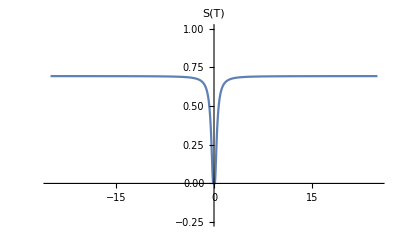

```mathematica
Plot[S[T], {T, -25, 25}, PlotLabel->"S(T)", PlotRange->{-.25,1}]
```

1d) Plot S(T) vs U(T). Explain maximum of U.

```mathematica
U[T_]:= (ϵ*Exp[-ϵ/(k*T)])/(1+Exp[-ϵ/(k*T)])
```

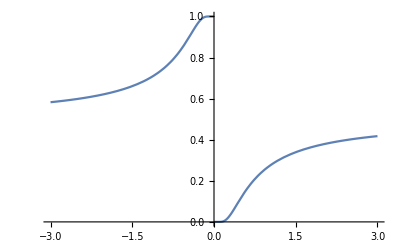

```mathematica
Plot[U[T],{T,-3,3}, PlotRange->{0,1}]
```

```mathematica
ParametricPlot[{S[T],U[T]}, {T, 0.25, 100}, AxesLabel->{"S(T)","U(T)"}]
```

-Graphics-